## Bounds on Scalar-Tensor Theory From GW151226

```mathematica
data1=Import[NotebookDirectory[]<>"/overall_post.csv","CSV"] (*Posterior containing cos_theta_inc,luminosity distance,right ascension, declination, m1_det,m2_det,spin_1,spin_2,cos_tilt1,cos_tilt2 respectively.*)
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195},52250,{0.795965,311.364,3.41712,-0.0397626,13.4479,9.18584,0.303922,0.287212,0.401218,0.583816}}
 |  |  |  |

```mathematica
data2=Import[NotebookDirectory[]<>"/-1pn-all-beta.csv","CSV"]  (*PPE beta*)
data3=Import[NotebookDirectory[]<>"/-1pn-all-alpha.csv","CSV"] (*PPE alpha*)
```

{{0.0000137661},{0.0000132674},{0.0000128066},{0.0000128773},{0.0000130833},{0.0000128252},{0.0000144412},52239,{0.0000155154},{0.0000234916},{0.0000137682},{0.0000130302},{0.0000130254},{0.0000127045}}
 |  |  |  |

{{0.0167435},{0.0169726},{0.0167368},{0.0168512},{0.016917},{0.016719},{0.0166968},52238,{0.0165277},{0.0166858},{0.0165886},{0.0168653},{0.0168797},{0.0168243},{0.0167868}}
 |  |  |  |

```mathematica
Length[data3]
```

52252

```mathematica
χ1=data1[[All,7]]; (*Dimensionles spin parameter*)
χ2=data1[[All,8]];
```

```mathematica
DL=data1[[All,2]]*10^6*3.261636*tyear/.tyear->3.1536*10^7
```

{2.52079×10^16,4.85528×10^16,6.35231×10^16,5.24927×10^16,3.73515×10^16,3.05455×10^16,4.78442×10^16,52238,3.80794×10^16,5.61282×10^16,5.43259×10^16,5.42488×10^16,3.54656×10^16,4.06701×10^16,3.20266×10^16}
 |  |  |  |

```mathematica
Clear[z]
```

```mathematica
Clear[z1,z2]
```

```mathematica
$Assumptions:=z1<1
```

```mathematica
A=Series[(ωM(1+z1)^3+ωΛ)^(-1/2),{z1,0,1}]//Normal
```

-(3 z1 ωM)/(2 (ωM+ωΛ)^(3/2))+1/(√(ωM+ωΛ))

```mathematica
B=(1+z)/H0 Integrate[A,{z1,0,z}]//Expand
```

-(3 z^2 ωM)/(4 H0 (ωM+ωΛ)^(3/2))-(3 z^3 ωM)/(4 H0 (ωM+ωΛ)^(3/2))+z/(H0 √(ωM+ωΛ))+z^2/(H0 √(ωM+ωΛ))

```mathematica
B2=Series[B,{z,0,2}]//Normal
```

z/(H0 √(ωM+ωΛ))+(z^2 (ωM+4 ωΛ))/(4 H0 (ωM+ωΛ)^(3/2))

```mathematica
Clear[z]
```

```mathematica
z=z/.Solve[B2-Dl==0,z][[2]]
```

(2 H0 (ωM+ωΛ)^(3/2) (-1/(H0 √(ωM+ωΛ))+√(1/(H0^2 (ωM+ωΛ))+(Dl (ωM+4 ωΛ))/(H0 (ωM+ωΛ)^(3/2)))))/(ωM+4 ωΛ)

```mathematica
z2=z/.{Dl->DL,ωM->0.3111,ωΛ->0.6889,α->0,H0->2.2683085*10^-18}
```

{0.054871,0.102135,0.130944,0.109823,0.0798379,0.0659518,0.100744,0.0844401,52237,0.0813074,0.116848,0.113374,0.113224,0.0760166,0.086514,0.0689964}
 |  |  |  |

```mathematica
m1=data1[[All,5]]/(1+z2)*tsolar/.tsolar->4.925491*10^-6 
(*Ligo posterior gives mass in detector frame. We have to convert it source frame*)
```

{0.0000737423,0.000052406,0.0000629487,0.0000589476,0.0000533338,0.0000668695,0.0000729009,52239,0.0000740165,0.000124027,0.0000656178,0.0000560597,0.0000650154,0.0000619624}
 |  |  |  |

```mathematica
m2=data1[[All,6]]/(1+z2)*tsolar/.tsolar->4.925491*10^-6
```

{0.0000381435,0.0000473271,0.0000378045,0.0000415688,0.0000478977,0.0000395864,0.0000351205,52239,0.0000331739,0.0000224433,0.0000371517,0.0000460789,0.0000400992,0.0000423245}
 |  |  |  |

```mathematica
η=(m1*m2)/(m1+m2)^2
```

{0.224692,0.249352,0.23443,0.242527,0.249279,0.233579,0.219419,0.205146,52237,0.181597,0.213704,0.129749,0.230819,0.247613,0.235953,0.241135}
 |  |  |  |

```mathematica
βppE=data2[[All,1]](*90% CL upper bound*)
αppE=data3[[All,1]](*90% CL upper bound*)
```

{0.0000137661,0.0000132674,0.0000128066,0.0000128773,0.0000130833,0.0000128252,0.0000144412,52238,0.0000199195,0.0000155154,0.0000234916,0.0000137682,0.0000130302,0.0000130254,0.0000127045}
 |  |  |  |

{0.0167435,0.0169726,0.0167368,0.0168512,0.016917,0.016719,0.0166968,0.0166076,52236,0.0167365,0.0165277,0.0166858,0.0165886,0.0168653,0.0168797,0.0168243,0.0167868}
 |  |  |  |

```mathematica
s1=(1+√(1-χ1^2))/2
s2=(1+√(1-χ2^2))/2
```

{0.940043,0.625779,0.956497,0.973489,0.925759,0.996231,0.900233,0.904313,52236,0.854346,0.912541,0.813523,0.791136,0.813935,0.998373,0.847153,0.976348}
 |  |  |  |

{0.997858,0.656355,0.876477,0.857439,0.925557,0.946235,0.99686,0.646782,52236,0.958547,0.669956,0.763379,0.993275,0.844423,0.88695,0.996893,0.978934}
 |  |  |  |

```mathematica
ϕdotSquared=Abs[-1792/5*η^(-2/5)/((m1*s1)-(m2*s2))^2*βppE]
```

{9.17464×10^6,2.76516×10^9,1.11852×10^7,1.72061×10^7,3.21486×10^8,9.67171×10^6,1.01279×10^7,52238,3.27513×10^6,8.46854×10^6,3.31407×10^6,1.82657×10^7,3.58038×10^7,3.64655×10^7,2.21306×10^7}
 |  |  |  |

```mathematica
√Mean[ϕdotSquared]//ScientificForm (*rough estimate*)
```

9.42813×10^5

```mathematica
ϕdotSquaredamp=Abs[-48/5*η^(-2/5)/((m1*s1)-(m2*s2))^2*αppE]
```

{2.98901×10^8,9.47517×10^10,3.91548×10^8,6.03106×10^8,1.11345×10^10,3.37716×10^8,3.13655×10^8,52238,7.27888×10^7,2.43948×10^8,6.26847×10^7,5.99315×10^8,1.24235×10^9,1.26162×10^9,7.83266×10^8}
 |  |  |  |

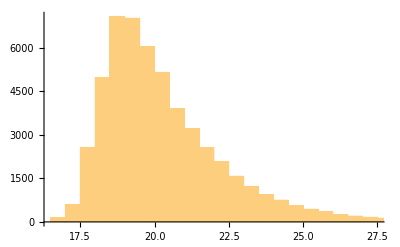

```mathematica
Histogram[Log[ϕdotSquaredamp]]
```

ϕ̇ from phase correction:

```mathematica
LogSquaredϕdotPhase=Log[ϕdotSquared] (*This is Log of sigma_(alpha^2)*)
```

{16.032,21.7404,16.2301,16.6608,19.5885,16.0847,16.1308,15.225,52236,16.5623,15.0019,15.9519,15.0137,16.7205,17.3936,17.4119,16.9125}
 |  |  |  |

```mathematica
Min[LogSquaredϕdotPhase]
```

13.8075

```mathematica
Max[LogSquaredϕdotPhase]
```

37.9563

```mathematica
𝒟logϕHist=HistogramDistribution[LogSquaredϕdotPhase]
```

DataDistribution[…]

```mathematica
𝒟logϕHist2=PDF[𝒟logϕHist,x];
```

```mathematica
𝒟logϕHist3[x_]=𝒟logϕHist2;
```

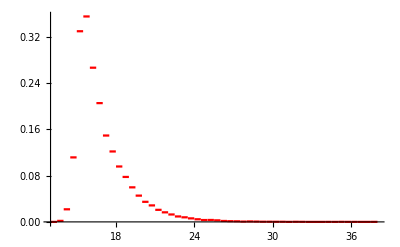

```mathematica
Plot1=Plot[𝒟logϕHist3[x],{x,13,38},PlotRange->All,PlotStyle->Red]
```

```mathematica
𝒟logϕdotSq=SmoothKernelDistribution[LogSquaredϕdotPhase]
```

DataDistribution[…]

```mathematica
𝒟logϕdotSq2=PDF[𝒟logϕdotSq,x]
```

Piecewise[{{InterpolatingFunction[…][x], 12.975≤x≤38.7888}, {0, True}}]

```mathematica
𝒟logϕdotSq3[x_]=𝒟logϕdotSq2
```

Piecewise[{{InterpolatingFunction[…][x], 12.975≤x≤38.7888}, {0, True}}]

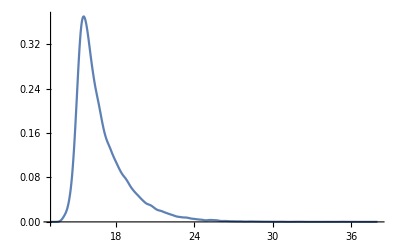

```mathematica
Plot2=Plot[𝒟logϕdotSq3[x],{x,13,38},PlotRange->All]
```

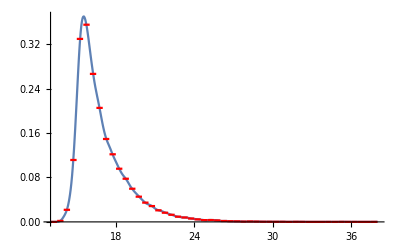

```mathematica
Show[Plot2,Plot1] (*SmoothKernelDistribution is not good enough. We need to interpolate the actual histogram*)
```

```mathematica
fun1αphase[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])]
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

```mathematica
ϕdotSqLogSample=Prepend[10^Range[-1,11,0.1],0]
```

{0,0.1,0.125893,0.158489,0.199526,0.251189,0.316228,0.398107,0.501187,0.630957,0.794328,1.,1.25893,1.58489,1.99526,2.51189,3.16228,3.98107,5.01187,6.30957,7.94328,10.,12.5893,15.8489,19.9526,25.1189,31.6228,39.8107,50.1187,63.0957,79.4328,100.,125.893,158.489,199.526,251.189,316.228,398.107,501.187,630.957,794.328,1000.,1258.93,1584.89,1995.26,2511.89,3162.28,3981.07,5011.87,6309.57,7943.28,10000.,12589.3,15848.9,19952.6,25118.9,31622.8,39810.7,50118.7,63095.7,79432.8,100000.,125893.,158489.,199526.,251189.,316228.,398107.,501187.,630957.,794328.,1.×10^6,1.25893×10^6,1.58489×10^6,1.99526×10^6,2.51189×10^6,3.16228×10^6,3.98107×10^6,5.01187×10^6,6.30957×10^6,7.94328×10^6,1.×10^7,1.25893×10^7,1.58489×10^7,1.99526×10^7,2.51189×10^7,3.16228×10^7,3.98107×10^7,5.01187×10^7,6.30957×10^7,7.94328×10^7,1.×10^8,1.25893×10^8,1.58489×10^8,1.99526×10^8,2.51189×10^8,3.16228×10^8,3.98107×10^8,5.01187×10^8,6.30957×10^8,7.94328×10^8,1.×10^9,1.25893×10^9,1.58489×10^9,1.99526×10^9,2.51189×10^9,3.16228×10^9,3.98107×10^9,5.01187×10^9,6.30957×10^9,7.94328×10^9,1.×10^10,1.25893×10^10,1.58489×10^10,1.99526×10^10,2.51189×10^10,3.16228×10^10,3.98107×10^10,5.01187×10^10,6.30957×10^10,7.94328×10^10,1.×10^11}

```mathematica
fun1ϕdotphaseTable[y_]=Table[{ϕdotSqLogSample[[i]],fun1αphase[ϕdotSqLogSample[[i]],y]},{i,1,Length[ϕdotSqLogSample]}];
```

```mathematica
ϕdotSqLogFinalPDFPhase=Table[{fun1ϕdotphaseTable[y][[i,1]],NIntegrate[fun1ϕdotphaseTable[y][[i,2]]*𝒟logϕdotSq3[y],{y,Min[ϕdotSqLogSample],Max[ϕdotSqLogSample]}]},{i,1,Length[fun1ϕdotphaseTable[y]]}]
```

{{0,4.67066×10^-8},{0.1,4.67066×10^-8},{0.125893,4.67066×10^-8},{0.158489,4.67066×10^-8},{0.199526,4.67066×10^-8},{0.251189,4.67066×10^-8},{0.316228,4.67066×10^-8},{0.398107,4.67066×10^-8},{0.501187,4.67066×10^-8},{0.630957,4.67066×10^-8},{0.794328,4.67066×10^-8},{1.,4.67066×10^-8},{1.25893,4.67066×10^-8},{1.58489,4.67066×10^-8},{1.99526,4.67066×10^-8},{2.51189,4.67066×10^-8},{3.16228,4.67066×10^-8},{3.98107,4.67066×10^-8},{5.01187,4.67066×10^-8},{6.30957,4.67066×10^-8},{7.94328,4.67066×10^-8},{10.,4.67066×10^-8},{12.5893,4.67066×10^-8},{15.8489,4.67066×10^-8},{19.9526,4.67066×10^-8},{25.1189,4.67066×10^-8},{31.6228,4.67066×10^-8},{39.8107,4.67066×10^-8},{50.1187,4.67066×10^-8},{63.0957,4.67066×10^-8},{79.4328,4.67066×10^-8},{100.,4.67066×10^-8},{125.893,4.67066×10^-8},{158.489,4.67066×10^-8},{199.526,4.67066×10^-8},{251.189,4.67066×10^-8},{316.228,4.67066×10^-8},{398.107,4.67066×10^-8},{501.187,4.67066×10^-8},{630.957,4.67066×10^-8},{794.328,4.67066×10^-8},{1000.,4.67066×10^-8},{1258.93,4.67066×10^-8},{1584.89,4.67066×10^-8},{1995.26,4.67066×10^-8},{2511.89,4.67066×10^-8},{3162.28,4.67065×10^-8},{3981.07,4.67065×10^-8},{5011.87,4.67065×10^-8},{6309.57,4.67065×10^-8},{7943.28,4.67064×10^-8},{10000.,4.67064×10^-8},{12589.3,4.67062×10^-8},{15848.9,4.6706×10^-8},{19952.6,4.67057×10^-8},{25118.9,4.67052×10^-8},{31622.8,4.67044×10^-8},{39810.7,4.67032×10^-8},{50118.7,4.67012×10^-8},{63095.7,4.66981×10^-8},{79432.8,4.66932×10^-8},{100000.,4.66854×10^-8},{125893.,4.6673×10^-8},{158489.,4.66535×10^-8},{199526.,4.66225×10^-8},{251189.,4.65736×10^-8},{316228.,4.64964×10^-8},{398107.,4.6375×10^-8},{501187.,4.61847×10^-8},{630957.,4.58885×10^-8},{794328.,4.54319×10^-8},{1.×10^6,4.47381×10^-8},{1.25893×10^6,4.37056×10^-8},{1.58489×10^6,4.22125×10^-8},{1.99526×10^6,4.01314×10^-8},{2.51189×10^6,3.73571×10^-8},{3.16228×10^6,3.38421×10^-8},{3.98107×10^6,2.96374×10^-8},{5.01187×10^6,2.49313×10^-8},{6.30957×10^6,2.00562×10^-8},{7.94328×10^6,1.54255×10^-8},{1.×10^7,1.1405×10^-8},{1.25893×10^7,8.19305×10^-9},{1.58489×10^7,5.791×10^-9},{1.99526×10^7,4.06902×10^-9},{2.51189×10^7,2.85921×10^-9},{3.16228×10^7,2.01408×10^-9},{3.98107×10^7,1.42356×10^-9},{5.01187×10^7,1.01001×10^-9},{6.30957×10^7,7.1892×10^-10},{7.94328×10^7,5.1244×10^-10},{1.×10^8,3.65093×10^-10},{1.25893×10^8,2.59776×10^-10},{1.58489×10^8,1.84551×10^-10},{1.99526×10^8,1.3085×10^-10},{2.51189×10^8,9.25524×10^-11},{3.16228×10^8,6.53172×10^-11},{3.98107×10^8,4.60463×10^-11},{5.01187×10^8,3.24691×10^-11},{6.30957×10^8,2.29139×10^-11},{7.94328×10^8,1.61853×10^-11},{1.×10^9,1.14435×10^-11},{1.25893×10^9,8.0946×10^-12},{1.58489×10^9,5.72081×10^-12},{1.99526×10^9,4.03603×10^-12},{2.51189×10^9,2.84444×10^-12},{3.16228×10^9,2.00507×10^-12},{3.98107×10^9,1.41357×10^-12},{5.01187×10^9,9.96327×10^-13},{6.30957×10^9,7.02935×10^-13},{7.94328×10^9,4.97207×10^-13},{1.×10^10,3.52743×10^-13},{1.25893×10^10,2.50994×10^-13},{1.58489×10^10,1.78917×10^-13},{1.99526×10^10,1.2734×10^-13},{2.51189×10^10,9.02119×10^-14},{3.16228×10^10,6.3641×10^-14},{3.98107×10^10,4.48915×10^-14},{5.01187×10^10,3.18105×10^-14},{6.30957×10^10,2.26922×10^-14},{7.94328×10^10,1.62913×10^-14},{1.×10^11,1.17394×10^-14}}

```mathematica
ϕdotSqLogFinalPDFPhaseInterp=Interpolation[ϕdotSqLogFinalPDFPhase]
```

InterpolatingFunction[…]

```mathematica
ϕdotSqNormalization=NIntegrate[ϕdotSqLogFinalPDFPhaseInterp[x],{x,Min[ϕdotSqLogSample],Max[ϕdotSqLogSample]}]
```

0.497224

```mathematica
ϕdotSqLogFinalPDFPhaseNorm=Table[{ϕdotSqLogFinalPDFPhase[[i,1]],ϕdotSqLogFinalPDFPhase[[i,2]]/ϕdotSqNormalization},{i,1,Length[ϕdotSqLogFinalPDFPhase]}];
```

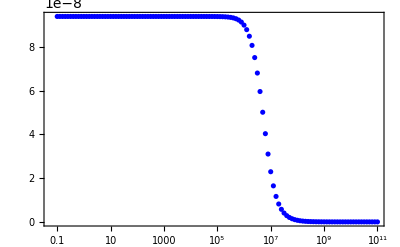

```mathematica
plotϕdotSqFinalPDFPhaseLogNorm=ListLogLinearPlot[{ϕdotSqLogFinalPDFPhaseNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red}]
```

```mathematica
ϕdotSqFinalPDFPhaseInterpLogNorm=Interpolation[ϕdotSqLogFinalPDFPhaseNorm]
```

InterpolatingFunction[…]

```mathematica
ϕdotSqFinalCDFPhaseNorm=Table[{ϕdotSqLogSample[[i]],NIntegrate[ϕdotSqFinalPDFPhaseInterpLogNorm[x],{x,Min[ϕdotSqLogSample],ϕdotSqLogSample[[i]]}]},{i,1,Length[ϕdotSqLogSample]}];
```

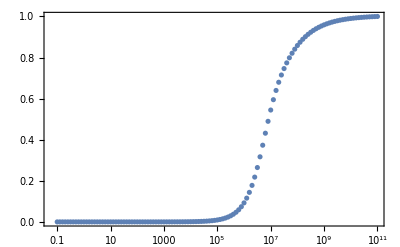

```mathematica
ListLogLinearPlot[ϕdotSqFinalCDFPhaseNorm,PlotRange->All,PlotRange->All,Frame->True]
```

```mathematica
ϕdotSqFinalCDFPhaseNormInterp=Interpolation[ϕdotSqFinalCDFPhaseNorm]
```

InterpolatingFunction[…]

```mathematica
ϕdotSq90CLphase=x/.FindRoot[ϕdotSqFinalCDFPhaseNormInterp[x]==0.9,{x,10^8}]
```

1.93291×10^8

```mathematica
√ϕdotSq90CLphase//ScientificForm
```

1.39029×10^4

```mathematica
ϕ̇ from amplitude correction:
```

```mathematica
LogSquaredϕdotamp=Log[ϕdotSquaredamp]
```

{19.5156,25.2745,19.7856,20.2176,23.1333,19.6377,19.5638,18.5183,52236,20.0602,18.1031,19.3125,17.9536,20.2113,20.9403,20.9557,20.479}
 |  |  |  |

```mathematica
Min[LogSquaredϕdotamp]
```

16.6175

```mathematica
Max[LogSquaredϕdotamp]
```

41.4733

```mathematica
Histogram[LogSquaredϕdotamp];
```

```mathematica
𝒟logϕdotSqamp=SmoothKernelDistribution[LogSquaredϕdotamp]
```

DataDistribution[…]

```mathematica
𝒟logϕdotSqamp2=PDF[𝒟logϕdotSqamp,x]
```

Piecewise[{{InterpolatingFunction[…][x], 15.6917≤x≤42.3991}, {0, True}}]

```mathematica
𝒟logϕdotSqamp3[x_]=𝒟logϕdotSqamp2
```

Piecewise[{{InterpolatingFunction[…][x], 15.6917≤x≤42.3991}, {0, True}}]

```mathematica
Plot2=Plot[𝒟logϕdotSqamp3[x],{x,7,40},PlotRange->All];
```

```mathematica
ϕdotSqLogSampleamp=Prepend[10^Range[-1,11,0.1],0];
```

```mathematica
fun1ϕdotampTable[y_]=Table[{ϕdotSqLogSampleamp[[i]],fun1αphase[ϕdotSqLogSampleamp[[i]],y]},{i,1,Length[ϕdotSqLogSampleamp]}];
```

```mathematica
ϕdotSqLogFinalPDFamp=Table[{fun1ϕdotampTable[y][[i,1]],NIntegrate[fun1ϕdotampTable[y][[i,2]]*𝒟logϕdotSqamp3[y],{y,Min[ϕdotSqLogSampleamp],Max[ϕdotSqLogSampleamp]}]},{i,1,Length[fun1ϕdotampTable[y]]}]
```

{{0,1.91217×10^-9},{0.1,1.91217×10^-9},{0.125893,1.91217×10^-9},{0.158489,1.91217×10^-9},{0.199526,1.91217×10^-9},{0.251189,1.91217×10^-9},{0.316228,1.91217×10^-9},{0.398107,1.91217×10^-9},{0.501187,1.91217×10^-9},{0.630957,1.91217×10^-9},{0.794328,1.91217×10^-9},{1.,1.91217×10^-9},{1.25893,1.91217×10^-9},{1.58489,1.91217×10^-9},{1.99526,1.91217×10^-9},{2.51189,1.91217×10^-9},{3.16228,1.91217×10^-9},{3.98107,1.91217×10^-9},{5.01187,1.91217×10^-9},{6.30957,1.91217×10^-9},{7.94328,1.91217×10^-9},{10.,1.91217×10^-9},{12.5893,1.91217×10^-9},{15.8489,1.91217×10^-9},{19.9526,1.91217×10^-9},{25.1189,1.91217×10^-9},{31.6228,1.91217×10^-9},{39.8107,1.91217×10^-9},{50.1187,1.91217×10^-9},{63.0957,1.91217×10^-9},{79.4328,1.91217×10^-9},{100.,1.91217×10^-9},{125.893,1.91217×10^-9},{158.489,1.91217×10^-9},{199.526,1.91217×10^-9},{251.189,1.91217×10^-9},{316.228,1.91217×10^-9},{398.107,1.91217×10^-9},{501.187,1.91217×10^-9},{630.957,1.91217×10^-9},{794.328,1.91217×10^-9},{1000.,1.91217×10^-9},{1258.93,1.91217×10^-9},{1584.89,1.91217×10^-9},{1995.26,1.91217×10^-9},{2511.89,1.91217×10^-9},{3162.28,1.91217×10^-9},{3981.07,1.91217×10^-9},{5011.87,1.91217×10^-9},{6309.57,1.91217×10^-9},{7943.28,1.91217×10^-9},{10000.,1.91217×10^-9},{12589.3,1.91217×10^-9},{15848.9,1.91217×10^-9},{19952.6,1.91217×10^-9},{25118.9,1.91217×10^-9},{31622.8,1.91217×10^-9},{39810.7,1.91217×10^-9},{50118.7,1.91217×10^-9},{63095.7,1.91216×10^-9},{79432.8,1.91216×10^-9},{100000.,1.91216×10^-9},{125893.,1.91216×10^-9},{158489.,1.91216×10^-9},{199526.,1.91215×10^-9},{251189.,1.91215×10^-9},{316228.,1.91214×10^-9},{398107.,1.91212×10^-9},{501187.,1.91209×10^-9},{630957.,1.91205×10^-9},{794328.,1.91199×10^-9},{1.×10^6,1.91188×10^-9},{1.25893×10^6,1.91171×10^-9},{1.58489×10^6,1.91145×10^-9},{1.99526×10^6,1.91103×10^-9},{2.51189×10^6,1.91036×10^-9},{3.16228×10^6,1.90931×10^-9},{3.98107×10^6,1.90765×10^-9},{5.01187×10^6,1.90504×10^-9},{6.30957×10^6,1.90092×10^-9},{7.94328×10^6,1.89448×10^-9},{1.×10^7,1.88448×10^-9},{1.25893×10^7,1.8691×10^-9},{1.58489×10^7,1.84581×10^-9},{1.99526×10^7,1.81136×10^-9},{2.51189×10^7,1.7619×10^-9},{3.16228×10^7,1.69353×10^-9},{3.98107×10^7,1.6031×10^-9},{5.01187×10^7,1.48895×10^-9},{6.30957×10^7,1.3517×10^-9},{7.94328×10^7,1.19507×10^-9},{1.×10^8,1.02642×10^-9},{1.25893×10^8,8.55661×10^-10},{1.58489×10^8,6.92786×10^-10},{1.99526×10^8,5.45653×10^-10},{2.51189×10^8,4.19171×10^-10},{3.16228×10^8,3.15337×10^-10},{3.98107×10^8,2.33457×10^-10},{5.01187×10^8,1.70847×10^-10},{6.30957×10^8,1.23977×10^-10},{7.94328×10^8,8.9388×10^-11},{1.×10^9,6.41377×10^-11},{1.25893×10^9,4.58856×10^-11},{1.58489×10^9,3.28017×10^-11},{1.99526×10^9,2.3459×10^-11},{2.51189×10^9,1.67791×10^-11},{3.16228×10^9,1.19882×10^-11},{3.98107×10^9,8.54889×10^-12},{5.01187×10^9,6.08276×10^-12},{6.30957×10^9,4.31764×10^-12},{7.94328×10^9,3.05675×10^-12},{1.×10^10,2.15881×10^-12},{1.25893×10^10,1.52239×10^-12},{1.58489×10^10,1.07345×10^-12},{1.99526×10^10,7.57389×10^-13},{2.51189×10^10,5.34807×10^-13},{3.16228×10^10,3.77975×10^-13},{3.98107×10^10,2.67318×10^-13},{5.01187×10^10,1.88987×10^-13},{6.30957×10^10,1.33403×10^-13},{7.94328×10^10,9.40363×10^-14},{1.×10^11,6.62757×10^-14}}

```mathematica
ϕdotSqLogFinalPDFampInterp=Interpolation[ϕdotSqLogFinalPDFamp]
```

InterpolatingFunction[…]

```mathematica
ϕdotSqNormalizationamp=NIntegrate[ϕdotSqLogFinalPDFampInterp[x],{x,Min[ϕdotSqLogSampleamp],Max[ϕdotSqLogSampleamp]}]
```

0.486316

```mathematica
ϕdotSqLogFinalPDFampNorm=Table[{ϕdotSqLogFinalPDFamp[[i,1]],ϕdotSqLogFinalPDFamp[[i,2]]/ϕdotSqNormalizationamp},{i,1,Length[ϕdotSqLogFinalPDFamp]}]
```

{{0,3.93194×10^-9},{0.1,3.93194×10^-9},{0.125893,3.93194×10^-9},{0.158489,3.93194×10^-9},{0.199526,3.93194×10^-9},{0.251189,3.93194×10^-9},{0.316228,3.93194×10^-9},{0.398107,3.93194×10^-9},{0.501187,3.93194×10^-9},{0.630957,3.93194×10^-9},{0.794328,3.93194×10^-9},{1.,3.93194×10^-9},{1.25893,3.93194×10^-9},{1.58489,3.93194×10^-9},{1.99526,3.93194×10^-9},{2.51189,3.93194×10^-9},{3.16228,3.93194×10^-9},{3.98107,3.93194×10^-9},{5.01187,3.93194×10^-9},{6.30957,3.93194×10^-9},{7.94328,3.93194×10^-9},{10.,3.93194×10^-9},{12.5893,3.93194×10^-9},{15.8489,3.93194×10^-9},{19.9526,3.93194×10^-9},{25.1189,3.93194×10^-9},{31.6228,3.93194×10^-9},{39.8107,3.93194×10^-9},{50.1187,3.93194×10^-9},{63.0957,3.93194×10^-9},{79.4328,3.93194×10^-9},{100.,3.93194×10^-9},{125.893,3.93194×10^-9},{158.489,3.93194×10^-9},{199.526,3.93194×10^-9},{251.189,3.93194×10^-9},{316.228,3.93194×10^-9},{398.107,3.93194×10^-9},{501.187,3.93194×10^-9},{630.957,3.93194×10^-9},{794.328,3.93194×10^-9},{1000.,3.93194×10^-9},{1258.93,3.93194×10^-9},{1584.89,3.93194×10^-9},{1995.26,3.93194×10^-9},{2511.89,3.93194×10^-9},{3162.28,3.93194×10^-9},{3981.07,3.93194×10^-9},{5011.87,3.93194×10^-9},{6309.57,3.93194×10^-9},{7943.28,3.93194×10^-9},{10000.,3.93194×10^-9},{12589.3,3.93194×10^-9},{15848.9,3.93194×10^-9},{19952.6,3.93194×10^-9},{25118.9,3.93194×10^-9},{31622.8,3.93194×10^-9},{39810.7,3.93194×10^-9},{50118.7,3.93194×10^-9},{63095.7,3.93194×10^-9},{79432.8,3.93194×10^-9},{100000.,3.93194×10^-9},{125893.,3.93193×10^-9},{158489.,3.93193×10^-9},{199526.,3.93192×10^-9},{251189.,3.93191×10^-9},{316228.,3.93188×10^-9},{398107.,3.93185×10^-9},{501187.,3.9318×10^-9},{630957.,3.93171×10^-9},{794328.,3.93157×10^-9},{1.×10^6,3.93135×10^-9},{1.25893×10^6,3.93101×10^-9},{1.58489×10^6,3.93047×10^-9},{1.99526×10^6,3.9296×10^-9},{2.51189×10^6,3.92824×10^-9},{3.16228×10^6,3.92608×10^-9},{3.98107×10^6,3.92266×10^-9},{5.01187×10^6,3.91728×10^-9},{6.30957×10^6,3.90882×10^-9},{7.94328×10^6,3.89558×10^-9},{1.×10^7,3.87501×10^-9},{1.25893×10^7,3.84338×10^-9},{1.58489×10^7,3.79551×10^-9},{1.99526×10^7,3.72466×10^-9},{2.51189×10^7,3.62295×10^-9},{3.16228×10^7,3.48237×10^-9},{3.98107×10^7,3.29642×10^-9},{5.01187×10^7,3.0617×10^-9},{6.30957×10^7,2.77947×10^-9},{7.94328×10^7,2.4574×10^-9},{1.×10^8,2.11061×10^-9},{1.25893×10^8,1.75948×10^-9},{1.58489×10^8,1.42456×10^-9},{1.99526×10^8,1.12201×10^-9},{2.51189×10^8,8.61931×10^-10},{3.16228×10^8,6.48421×10^-10},{3.98107×10^8,4.80053×10^-10},{5.01187×10^8,3.51309×10^-10},{6.30957×10^8,2.5493×10^-10},{7.94328×10^8,1.83806×10^-10},{1.×10^9,1.31885×10^-10},{1.25893×10^9,9.43535×10^-11},{1.58489×10^9,6.74494×10^-11},{1.99526×10^9,4.82383×10^-11},{2.51189×10^9,3.45024×10^-11},{3.16228×10^9,2.46511×10^-11},{3.98107×10^9,1.75789×10^-11},{5.01187×10^9,1.25078×10^-11},{6.30957×10^9,8.87825×10^-12},{7.94328×10^9,6.28552×10^-12},{1.×10^10,4.43911×10^-12},{1.25893×10^10,3.13046×10^-12},{1.58489×10^10,2.20732×10^-12},{1.99526×10^10,1.5574×10^-12},{2.51189×10^10,1.09971×10^-12},{3.16228×10^10,7.77222×10^-13},{3.98107×10^10,5.49681×10^-13},{5.01187×10^10,3.8861×10^-13},{6.30957×10^10,2.74314×10^-13},{7.94328×10^10,1.93365×10^-13},{1.×10^11,1.36281×10^-13}}

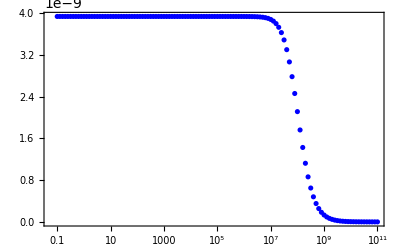

```mathematica
plotϕdotSqFinalPDFampLogNorm=ListLogLinearPlot[{ϕdotSqLogFinalPDFampNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red}]
```

```mathematica
ϕdotSqFinalPDFampInterpLogNorm=Interpolation[ϕdotSqLogFinalPDFampNorm]
```

InterpolatingFunction[…]

```mathematica
ϕdotSqFinalCDFampNorm=Table[{ϕdotSqLogSampleamp[[i]],NIntegrate[ϕdotSqFinalPDFampInterpLogNorm[x],{x,Min[ϕdotSqLogSampleamp],ϕdotSqLogSampleamp[[i]]}]},{i,1,Length[ϕdotSqLogSampleamp]}]
```

{{0,0},{0.1,3.93194×10^-10},{0.125893,4.95002×10^-10},{0.158489,6.23171×10^-10},{0.199526,7.84526×10^-10},{0.251189,9.87659×10^-10},{0.316228,1.24339×10^-9},{0.398107,1.56533×10^-9},{0.501187,1.97064×10^-9},{0.630957,2.48089×10^-9},{0.794328,3.12325×10^-9},{1.,3.93194×10^-9},{1.25893,4.95002×10^-9},{1.58489,6.23171×10^-9},{1.99526,7.84526×10^-9},{2.51189,9.87659×10^-9},{3.16228,1.24339×10^-8},{3.98107,1.56533×10^-8},{5.01187,1.97064×10^-8},{6.30957,2.48089×10^-8},{7.94328,3.12325×10^-8},{10.,3.93194×10^-8},{12.5893,4.95002×10^-8},{15.8489,6.23171×10^-8},{19.9526,7.84526×10^-8},{25.1189,9.87659×10^-8},{31.6228,1.24339×10^-7},{39.8107,1.56533×10^-7},{50.1187,1.97064×10^-7},{63.0957,2.48089×10^-7},{79.4328,3.12325×10^-7},{100.,3.93194×10^-7},{125.893,4.95002×10^-7},{158.489,6.23171×10^-7},{199.526,7.84526×10^-7},{251.189,9.87659×10^-7},{316.228,1.24339×10^-6},{398.107,1.56533×10^-6},{501.187,1.97064×10^-6},{630.957,2.48089×10^-6},{794.328,3.12325×10^-6},{1000.,3.93194×10^-6},{1258.93,4.95002×10^-6},{1584.89,6.23171×10^-6},{1995.26,7.84526×10^-6},{2511.89,9.87659×10^-6},{3162.28,0.0000124339},{3981.07,0.0000156533},{5011.87,0.0000197064},{6309.57,0.0000248089},{7943.28,0.0000312325},{10000.,0.0000393194},{12589.3,0.0000495002},{15848.9,0.0000623171},{19952.6,0.0000784526},{25118.9,0.0000987659},{31622.8,0.000124339},{39810.7,0.000156533},{50118.7,0.000197064},{63095.7,0.000248089},{79432.8,0.000312325},{100000.,0.000393194},{125893.,0.000495002},{158489.,0.00062317},{199526.,0.000784524},{251189.,0.000987656},{316228.,0.00124338},{398107.,0.00156532},{501187.,0.00197062},{630957.,0.00248084},{794328.,0.00312316},{1.×10^6,0.00393175},{1.25893×10^6,0.00494963},{1.58489×10^6,0.00623093},{1.99526×10^6,0.0078437},{2.51189×10^6,0.00987349},{3.16228×10^6,0.0124277},{3.98107×10^6,0.015641},{5.01187×10^6,0.0196818},{6.30957×10^6,0.02476},{7.94328×10^6,0.0311354},{1.×10^7,0.0391271},{1.25893×10^7,0.0491209},{1.58489×10^7,0.0615733},{1.99526×10^7,0.0770071},{2.51189×10^7,0.0959919},{3.16228×10^7,0.119104},{3.98107×10^7,0.14686},{5.01187×10^7,0.179627},{6.30957×10^7,0.217507},{7.94328×10^7,0.260232},{1.×10^8,0.307099},{1.25893×10^8,0.357015},{1.58489×10^8,0.408627},{1.99526×10^8,0.460494},{2.51189×10^8,0.511261},{3.16228×10^8,0.559819},{3.98107×10^8,0.605409},{5.01187×10^8,0.64763},{6.30957×10^8,0.686348},{7.94328×10^8,0.721594},{1.×10^9,0.753503},{1.25893×10^9,0.782275},{1.58489×10^9,0.808173},{1.99526×10^9,0.831482},{2.51189×10^9,0.852471},{3.16228×10^9,0.871362},{3.98107×10^9,0.888339},{5.01187×10^9,0.903564},{6.30957×10^9,0.917185},{7.94328×10^9,0.929342},{1.×10^10,0.940163},{1.25893×10^10,0.949775},{1.58489×10^10,0.958307},{1.99526×10^10,0.965882},{2.51189×10^10,0.972614},{3.16228×10^10,0.9786},{3.98107×10^10,0.983929},{5.01187×10^10,0.988673},{6.30957×10^10,0.992893},{7.94328×10^10,0.99664},{1.×10^11,1.}}

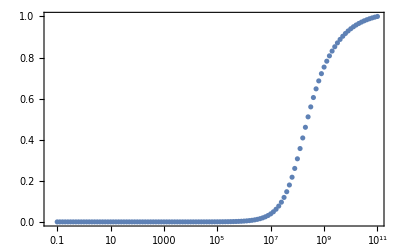

```mathematica
ListLogLinearPlot[ϕdotSqFinalCDFampNorm,PlotRange->All,PlotRange->All,Frame->True]
```

```mathematica
ϕdotSqFinalCDFampNormInterp=Interpolation[ϕdotSqFinalCDFampNorm]
```

InterpolatingFunction[…]

```mathematica
ϕdotSq90CLamp=x/.FindRoot[ϕdotSqFinalCDFampNormInterp[x]==0.9,{x,10^9}]
```

4.73478×10^9

```mathematica
√ϕdotSq90CLamp//ScientificForm
```

6.88098×10^4

## Small Coupling approximation:

```mathematica
𝒟log=HistogramDistribution[Log[√ϕdotSquared*m1]] (*simga_zeta from log of phase correction from monte-carlo. If we use the distribution of ζ, the pdf we get looks almost rectangular. That is why we are using the log[sigma_zeta]. We can compare their shapes from following two histograms *)
```

DataDistribution[…]

```mathematica
√ϕdotSquared*m1
```

{0.223363,2.75576,0.210527,0.244516,0.956277,0.20796,0.232003,0.164412,52236,0.272045,0.16912,0.215394,0.225785,0.28044,0.33544,0.392606,0.291491}
 |  |  |  |

```mathematica
Histogram[Log[√ϕdotSquared*m1]];
```

```mathematica
ps1=PDF[𝒟log,x];
```

```mathematica
ps2[x]=ps1;
```

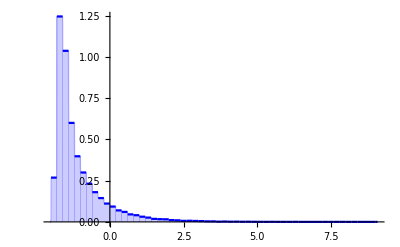

```mathematica
plot3=Plot[ps2[x],{x,Log[Min[√ϕdotSquared*m1]],Log[Max[√ϕdotSquared*m1]]},Filling->Axis,PlotStyle->Blue,PlotRange->All]
```

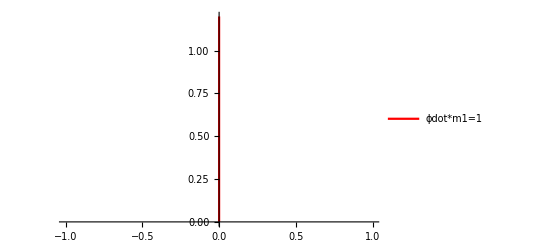

```mathematica
zeta1=ListLinePlot[{{0,0},{0,1.2}},PlotStyle->Red,PlotLegends->{Placed[LineLegend[{"ϕdot*m1=1"},LabelStyle->{Orange,FontSize->10},LegendMarkerSize->8,LegendMargins->0,LegendFunction->"Frame"],{Right,Top}]}]
```

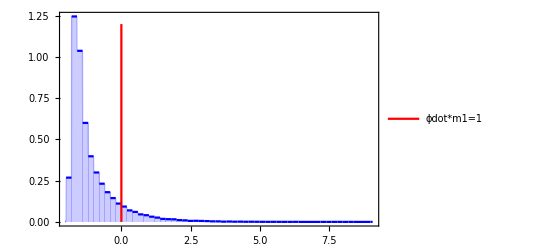

```mathematica
Show[plot3,zeta1,Frame->True,PlotRange->All] (*Shows how much of the area under the curve satisfies small coupling approximation*)
```

```mathematica
Integrate[ps2[x],{x,Log[Min[√ϕdotSquared*m1]],0}] (*90% satisfies small coupling approximation with 90% CL*)
```

0.903752

```mathematica
Integrate[ps2[x],{x,-Infinity,Infinity}]
```

1.

```mathematica
Min[Log[m1*√ϕdotSquaredamp]]
```

-0.206765

```mathematica
𝒟logamp=HistogramDistribution[Log[m1*√ϕdotSquaredamp]]
```

DataDistribution[…]

```mathematica
ps1amp=PDF[𝒟logamp,x];
ps2amp[x]=ps1amp;
```

```mathematica
Min[Log[m1*√ϕdotSquaredamp]]
```

-0.365624

```mathematica
Max[Log[m1*√ϕdotSquaredamp]]
```

10.8354

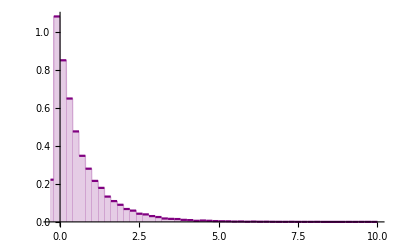

```mathematica
Plot[ps2amp[x],{x,-0.3,10},Filling->Axis,PlotStyle->Purple,PlotRange->All]
```

```mathematica
Integrate[ps2amp[x],{x,Log[Min[m1*√ϕdotSquaredamp]],Log[Max[m1*√ϕdotSquaredamp]]}]
```

0.992366

```mathematica
Integrate[ps2amp[x],{x,Log[Min[m1*√ϕdotSquaredamp]],0}] (*25% satisfies small coupling approximation*)
```

0.252506